MatrixForm

Null

Null

Null

«5 more identical outputs»

m w^2 x[t]+2 m w y'[t]

Null

Null

(98 (0.4 t Cos[0.4 t]-Sin[0.4 t])
-98 (Cos[0.4 t]+0.4 t Sin[0.4 t]))

Null

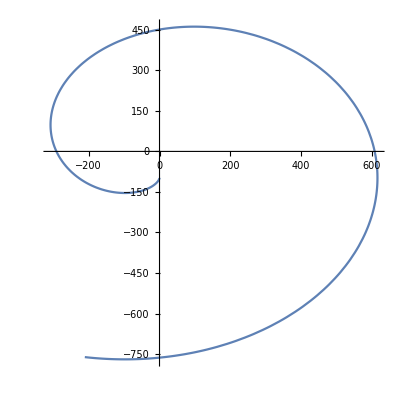

Null

Null

Null

```mathematica
(*Construct the r vector and velocity vector functions.*)
$Post = MatrixForm
rvec[t_] = {x[t],y[t]};
Vvec[t_] = D[rvec[t],t];
rvec3D = {x[t],y[t],0};
wvec = {0,0,w};
(*Gravity Definition*)
g = 9.81;
(*Here we define the centrifugal acceleration at distance R from the point of rotation*)
forceAtEdge = .3 * g * m;
(*what is the length of the vector that is perpendicular to the axis of rotation and connects the axis of rotation to the edge of the ship*)

(*Our ficticious forces*)
Fcent = - m (Cross[wvec,Cross[wvec,rvec3D]]);
Fcor = -2 m Cross[wvec,D[rvec3D,t]];
Dot[(Fcent + Fcor),{1,0,0}]
(*Now Begin Work on the problem*)
(*Determine start position as d*)
result =FullSimplify[ExpToTrig[DSolve[{x''[t]==Dot[(Fcent + Fcor)/m,{1,0,0}],y''[t] == Dot[(Fcent + Fcor)/m,{0,1,0}],x'[0] == 0, x[0]== 0, y'[0] == 0, y[0] == -d},{x[t],y[t]},t]]];
(*Solve for the correct Parameters given the initial inputs*)
params = {R -> 100, d -> 98, w -> .4};
(*Parametric Plot*)
{(x[t]/.result)/. params,(y[t]/.result)/. params}
pt[t_] = {98 (0.4 t Cos[0.4 t]-Sin[0.4 t]),-98 (Cos[0.4 t]+0.4 t Sin[0.4 t])};
curve = ParametricPlot[pt[t],{t,0,20}, AspectRatio->1] 
circle = With[{r = 200} , {
{Opacity[.1],Blue,Disk[{0,0},r]},
{Opacity[.15],Blue,
Table[Line[{{x,-Sqrt[r^2-x^2]},{x,+Sqrt[r^2-x^2]}}],{x,-r,r,r/10}],
Table[Line[{{-Sqrt[r^2-y^2],y},{+Sqrt[r^2-y^2],y}}],{y,-r,r,r/10}]
}}];
graphicsobjects = {circle,curve[[1]]};
Graphics[ graphicsobjects];
Animate[Graphics[{graphicsobjects,{Black,PointSize[.03],Point[{pt[t]}]}}],{t,0,20}]
```

```mathematica
(*I now want to create a force field texture to import into blender. 
-red is x axis,green is y axis, blue is z axis
- .5 is no force, greater than .5 is negative axis direction, less than .5 is acc in positive z axis*)
pixLen = 400;
pixWidth = 400;

Reap[
	Sow[1]]

Reap[For[i=1,i<=10,i++,Sow[i];Sow[7];Sow[i!];Sow[N@Log@i]];][[2,1]]~Partition~4
imgArr = {{{1,0,0},{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{1,0,0},{0,1,0},{0,0,1}}}
Image[imgArr,ColorSpace->"RGB"]
```

Null

Null

(1
{{1}})

(1 | 7 | 1 | 0.
2 | 7 | 2 | 0.693147
3 | 7 | 6 | 1.09861
4 | 7 | 24 | 1.38629
5 | 7 | 120 | 1.60944
6 | 7 | 720 | 1.79176
7 | 7 | 5040 | 1.94591
8 | 7 | 40320 | 2.07944
9 | 7 | 362880 | 2.19722
10 | 7 | 3628800 | 2.30259)

((1
0
0) | (1
0
0) | (0
1
0) | (0
0
1)
(1
0
0) | (1
0
0) | (0
1
0) | (0
0
1)
(1
0
0) | (1
0
0) | (0
1
0) | (0
0
1)
(1
0
0) | (1
0
0) | (0
1
0) | (0
0
1)
(1
0
0) | (1
0
0) | (0
1
0) | (0
0
1))

-Graphics-

```mathematica
Dimensions[{{98 (0.4 t Cos[0.4 t]-Sin[0.4 t])},{-98 (Cos[0.4 t]+0.4 t Sin[0.4 t])}}]
```

(2
1)

```mathematica
Times@@{2,1}
```

2